```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\GitHub\collab-optimizer\data

## Simplified data files from Python sim

```mathematica
tauList=Range[80,120,5];
numRuns=100;
runTime=1000;
```

```mathematica
meanCollabRate=(Mean@Flatten@Import["microsim-theta_1.0-tau_"<>ToString[#]<>"-runtime_1000.txt","Table"]&/@tauList)/(runTime/60)
```

{1251/25,1251/25,1251/25,1251/25,218973/5000,297/1000,3/10,3/10,3/10}

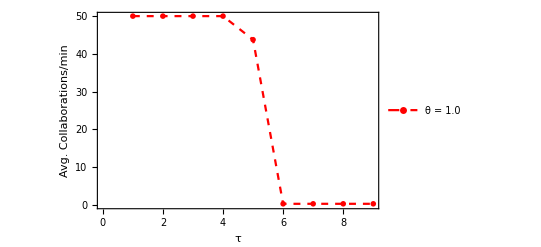

```mathematica
origCollabPlot=ListPlot[meanCollabRate,Joined->True,PlotMarkers->{Automatic,Large},PlotStyle->Directive[Thick,Dashed,Red],Frame->{True,True,False,False},FrameLabel->{"τ","Avg. Collaborations/min"},PlotLegends->{"θ = 1.0"}, PlotRange->{Automatic,Automatic}]
```

## Plot data from Python collab-sim

```mathematica
numRuns=10;
runMins=1000/60;
```

### Original collaboration experiments

```mathematica
AvgSimRunDat[θ_,τ_,runMins_,numRuns_]:=Module[{sdat},
Mean[(sdat=<<("microsim-theta_"<>θ<>"-tau_"<>τ<>"-run_"<>ToString[#]<>".txt");
Length@Cases[SplitBy[sdat,Last],Except[{___,{_,0},___}]])&/@Range[1,numRuns]]/runMins
]
```

```mathematica
processSimDat=Table[{ToExpression[τ],AvgSimRunDat[θ,τ,runMins,numRuns]},{θ,{"1.0"}},{τ,{"5","8","9","10","11","12","15"}}];
```

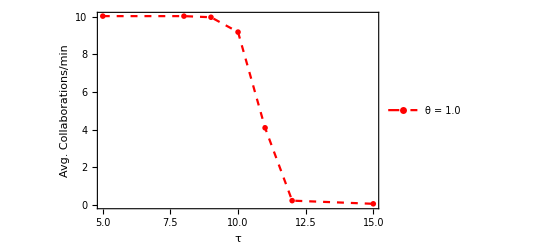

```mathematica
origCollabPlot=ListPlot[processSimDat,Joined->True,PlotMarkers->{Automatic,Large},PlotStyle->Directive[Thick,Dashed,Red],Frame->{True,True,False,False},FrameLabel->{"τ","Avg. Collaborations/min"},PlotLegends->{"θ = 1.0"}, PlotRange->{Automatic,Automatic}]
```

### Noisy Sensing collaboration experiments

```mathematica
AvgNoisySimRunDat[sigNoiseMean_,sigNoiseSD_,sensorNoiseSD_,runMins_,numRuns_]:=Module[{sdat},
Mean[(sdat=<<("noisysim-sigmean_"<>sigNoiseMean<>"-signoisesd_"<>sigNoiseSD<>"-sensorsd_"<>sensorNoiseSD<>"-run_"<>ToString[#]<>".txt");
Length@Cases[SplitBy[sdat,Last],Except[{___,{_,0},___}]])&/@Range[1,numRuns]]/runMins
]
```

```mathematica
processNoisySimDat=Table[{ToExpression[sigNoiseMean],AvgNoisySimRunDat[sigNoiseMean,sigNoiseSD,sensorNoiseSD,runMins,numRuns]},{sensorNoiseSD,{"0.1","1.0","2.0","5.0","10.0"}},{sigNoiseSD,{"0.1","1.0","2.0","5.0","10.0"}},{sigNoiseMean,{"5","8","9","10","11","12","15"}}];
```

```mathematica
processNoisySimDat//Dimensions
```

{5,5,7,2}

```mathematica
processNoisySimDat⟦1,2⟧
```

{{5,501/50},{8,501/50},{9,4947/500},{10,3711/500},{11,651/125},{12,531/250},{15,3/50}}

```mathematica
drawNoisyExpPlot[IDsigNoiseSD_,IDsensorNoiseSD_]:=Module[{sensorNoiseSD={"0.1","1.0","2.0","5.0","10.0"},sigNoiseSD={"0.1","1.0","2.0","5.0","10.0"}},
ListPlot[processNoisySimDat⟦IDsensorNoiseSD,IDsigNoiseSD⟧,Joined->True,PlotMarkers->{Automatic,Large},PlotStyle->Directive[Thick],Frame->{True,True,False,False},FrameLabel->{"(Red) τ\n(Blue) Signal Noise Mean","Avg. Collaborations/min"},PlotLabel->("Signal Noise SD = "<>sigNoiseSD⟦IDsigNoiseSD⟧<>"\nSensor Noise SD = "<>sensorNoiseSD⟦IDsensorNoiseSD⟧),BaseStyle->FontSize->16,PlotRange->{Automatic,{0,11}},ImageSize->{500,500}]]
```

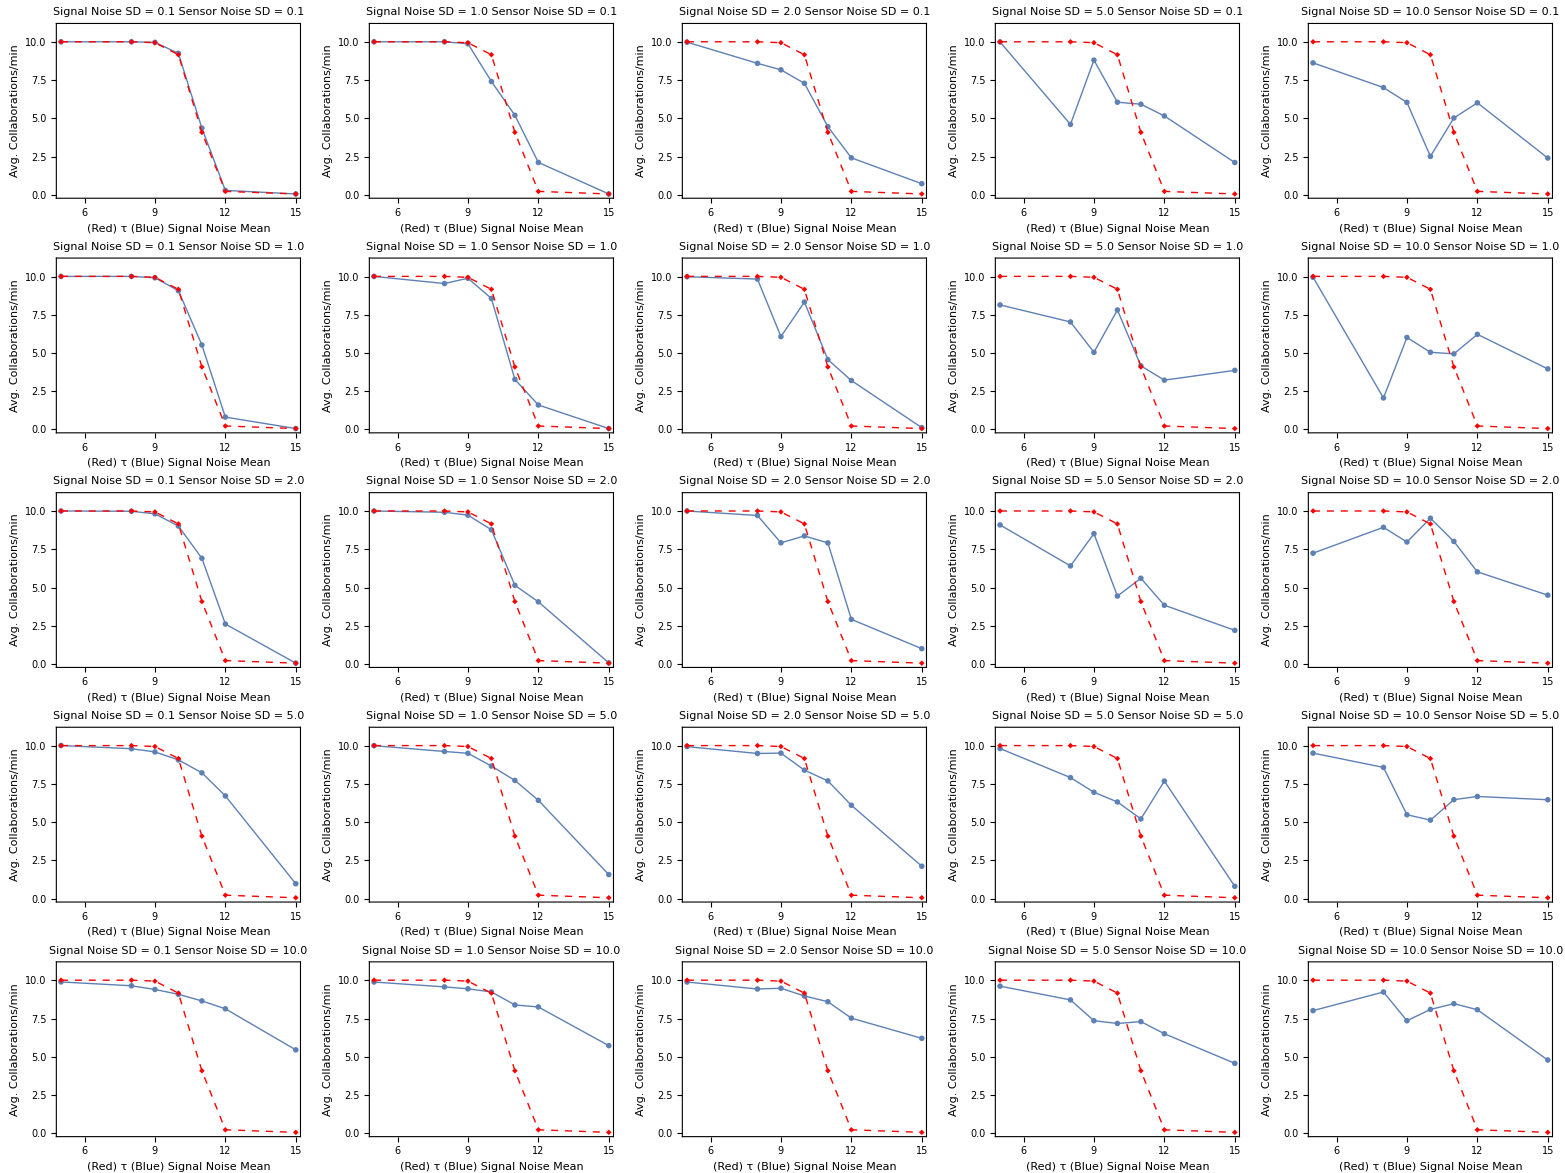

```mathematica
origPlotSimple=ListPlot[processSimDat,Joined->True,PlotMarkers->{"◆",Medium},PlotStyle->Directive[Thick,Dashed,Red]];
Table[Show[drawNoisyExpPlot[IDsigNoiseSD,IDsensorNoiseSD],origPlotSimple],{IDsensorNoiseSD,1,5},{IDsigNoiseSD,1,5}]//Grid
```

```mathematica
?MapThread
```

MapThread[f,{{a_1,a_2,…},{b_1,b_2,…},…}] gives {f[a_1,b_1,…],f[a_2,b_2,…],…}. 
MapThread[f,{expr_1,expr_2,…},n] applies f to the parts of the expr_i at level n.

```mathematica
processNoisySimDat⟦1,2,1⟧
```

{{5,167/30},{8,167/30},{9,1661/300},{10,761/150},{11,184/75},{12,37/150},{15,1/30}}

## Data from real Droplet experiments

```mathematica
AvgRealRunDat[θ_,τ_]:=Module[{dat},
dat[θ,τ]=<<("task_alloc_"<>τ<>"_"<>θ<>".txt");
Length[Select[SplitBy[dat[θ,τ],Last[#]≥4&],MemberQ[Last[Transpose[#]],x_/;x≥ 4]&]]/30]
```

```mathematica
processRealDat=Table[{ToExpression[τ],AvgRealRunDat[θ,τ]},{θ,{"0.1","1.0","10.0"}},{τ,{"2","3","4","5","6"}}]
```

{{{2,139/15},{3,79/10},{4,87/10},{5,259/30},{6,118/15}},{{2,271/30},{3,73/10},{4,76/15},{5,74/15},{6,149/30}},{{2,23/5},{3,37/6},{4,38/5},{5,21/5},{6,21/10}}}

## Overlay data plots

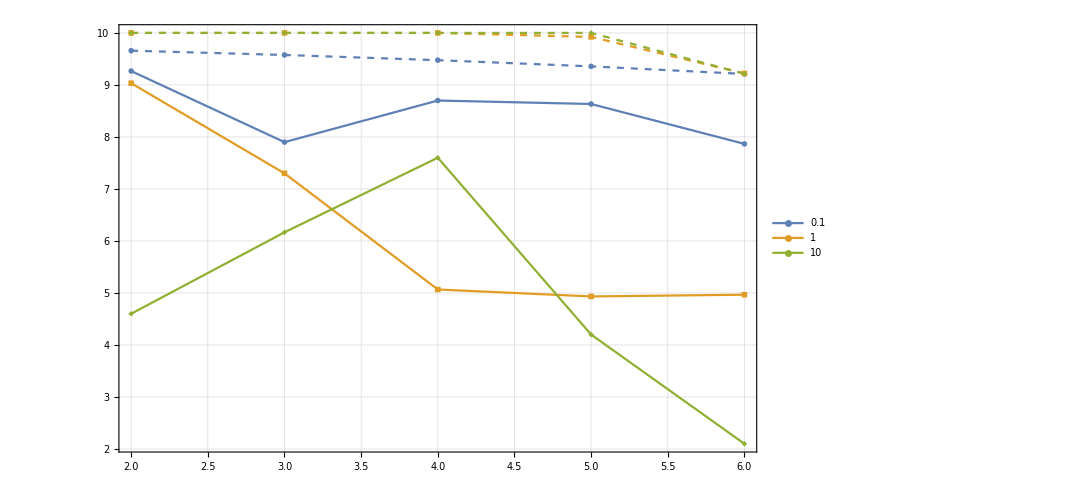

```mathematica
Show[ListPlot[processRealDat,Joined->True,PlotMarkers->{Automatic,Large},PlotStyle->Directive[Thick],PlotTheme->"Detailed",ImageSize->800,PlotLegends->{0.1,1,10},PlotRange->{Automatic,{11,2}}],ListPlot[processSimDat,Joined->True,PlotMarkers->{Automatic,Large},PlotStyle->Directive[Thick,Dashed]]]
```